## Problem

### 2 dim

```mathematica
Q=1;
Z=1;
G={2,3};
Subscript[σ, rel]=0.2;
Subscript[σ, abs]=0.2;
```

```mathematica
u[x_]:=(Q*G*x)/(Z+Total[x])-x
v[x1_,x2_]:=Evaluate@{
-D[u[{x1,x2}][[1]],x1]//FullSimplify,
-D[u[{x1,x2}][[2]],x2]//FullSimplify}
V[vec_]:=v@@vec
v[x1,x2]
V[{1,1}]
```

{1-(2 (1+x2))/(1+x1+x2)^2,1-(3 (1+x1))/(1+x1+x2)^2}

{5/9,1/3}

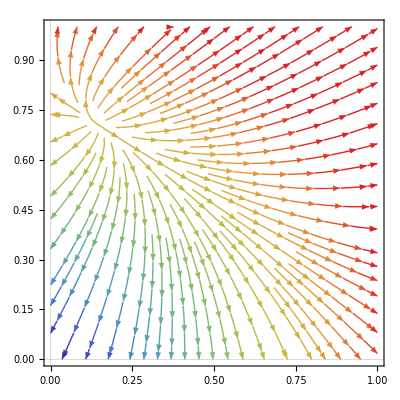

```mathematica
StreamPlot[v[x,y],{x,0,1},{y,0,1},StreamColorFunction->(ColorData["Rainbow",Norm[{#1,#2}]]&),
PlotTheme->"Scientific"]
```

```mathematica
equilibriumData=NSolve[
v[x,y]⟦1⟧==0&&
v[x,y]⟦2⟧==0&&
0≤x &&
0≤y,
{x,y}];
equilibriumPointData=Table[{x,y}/.point,{point,equilibriumData}]
```

{{0.1396,0.7094}}

### 4 dim

```mathematica
Q=1000;
Z=100;
G={1.8,2.0,2.2,2.4};
```

```mathematica
u[x_]:=(Q*G*x)/(Z+Total[x])-x
V[x1_,x2_,x3_,x4_]:=Evaluate@{
-D[u[{x1,x2,x3,x4}][[1]],x1]//FullSimplify,
-D[u[{x1,x2,x3,x4}][[2]],x2]//FullSimplify,
-D[u[{x1,x2,x3,x4}][[3]],x3]//FullSimplify,
-D[u[{x1,x2,x3,x4}][[4]],x4]//FullSimplify
}
V[vec_]:=V@@vec;
V[x1,x2,x3,x4]
```

{1+(-180000.-1800. x2-1800. x3-1800. x4)/(100.+x1+x2+x3+x4)^2,1+(-200000.-2000. x1-2000. x3-2000. x4)/(100.+x1+x2+x3+x4)^2,1+(-220000.-2200. x1-2200. x2-2200. x4)/(100.+x1+x2+x3+x4)^2,1+(-240000.-2400. x1-2400. x2-2400. x3)/(100.+x1+x2+x3+x4)^2}

```mathematica
equilibriumData=NSolve[
V[x1,x2,x3,x4]⟦1⟧==0&&
V[x1,x2,x3,x4]⟦2⟧==0&&
V[x1,x2,x3,x4]⟦3⟧==0&&
V[x1,x2,x3,x4]⟦4⟧==0&&
0≤x1 &&
0≤x2 &&
0≤x3 &&
0≤x4,
{x1,x2,x3,x4}];
equilibriumPointData=Table[{x1,x2,x3,x4}/.point,{point,equilibriumData}]
```

{{185.76,326.15,441.015,536.735}}

### N dim

```mathematica
Clear[x]
```

```mathematica
u[x_]:=(Q*G*x)/(Z+Total[x])-x
n=10;
Q=1000;
Z=100;
G=Table[6.0+i*0.1/n,{i,1,n}]
var=Array[x,n]
V=Evaluate@Table[-D[u[var][[i]],var[[i]]]//FullSimplify,{i,1,n}]
```

{6.01,6.02,6.03,6.04,6.05,6.06,6.07,6.08,6.09,6.1}

{x[1],x[2],x[3],x[4],x[5],x[6],x[7],x[8],x[9],x[10]}

{1+(6010. x[1]-6010. (100.+x[1]+x[2]+x[3]+x[4]+x[5]+x[6]+x[7]+x[8]+x[9]+x[10]))/(100.+x[1]+x[2]+x[3]+x[4]+x[5]+x[6]+x[7]+x[8]+x[9]+x[10])^2,1+(6020. x[2]-6020. (100.+x[1]+x[2]+x[3]+x[4]+x[5]+x[6]+x[7]+x[8]+x[9]+x[10]))/(100.+x[1]+x[2]+x[3]+x[4]+x[5]+x[6]+x[7]+x[8]+x[9]+x[10])^2,1+(6030. x[3]-6030. (100.+x[1]+x[2]+x[3]+x[4]+x[5]+x[6]+x[7]+x[8]+x[9]+x[10]))/(100.+x[1]+x[2]+x[3]+x[4]+x[5]+x[6]+x[7]+x[8]+x[9]+x[10])^2,1+(6040. x[4]-6040. (100.+x[1]+x[2]+x[3]+x[4]+x[5]+x[6]+x[7]+x[8]+x[9]+x[10]))/(100.+x[1]+x[2]+x[3]+x[4]+x[5]+x[6]+x[7]+x[8]+x[9]+x[10])^2,1+(6050. x[5]-6050. (100.+x[1]+x[2]+x[3]+x[4]+x[5]+x[6]+x[7]+x[8]+x[9]+x[10]))/(100.+x[1]+x[2]+x[3]+x[4]+x[5]+x[6]+x[7]+x[8]+x[9]+x[10])^2,1+(6060. x[6]-6060. (100.+x[1]+x[2]+x[3]+x[4]+x[5]+x[6]+x[7]+x[8]+x[9]+x[10]))/(100.+x[1]+x[2]+x[3]+x[4]+x[5]+x[6]+x[7]+x[8]+x[9]+x[10])^2,1+(6070. x[7]-6070. (100.+x[1]+x[2]+x[3]+x[4]+x[5]+x[6]+x[7]+x[8]+x[9]+x[10]))/(100.+x[1]+x[2]+x[3]+x[4]+x[5]+x[6]+x[7]+x[8]+x[9]+x[10])^2,1+(6080. x[8]-6080. (100.+x[1]+x[2]+x[3]+x[4]+x[5]+x[6]+x[7]+x[8]+x[9]+x[10]))/(100.+x[1]+x[2]+x[3]+x[4]+x[5]+x[6]+x[7]+x[8]+x[9]+x[10])^2,1+(6090. x[9]-6090. (100.+x[1]+x[2]+x[3]+x[4]+x[5]+x[6]+x[7]+x[8]+x[9]+x[10]))/(100.+x[1]+x[2]+x[3]+x[4]+x[5]+x[6]+x[7]+x[8]+x[9]+x[10])^2,1+(6100. x[10]-6100. (100.+x[1]+x[2]+x[3]+x[4]+x[5]+x[6]+x[7]+x[8]+x[9]+x[10]))/(100.+x[1]+x[2]+x[3]+x[4]+x[5]+x[6]+x[7]+x[8]+x[9]+x[10])^2}

```mathematica
equilibriumData=NSolve[
Fold[#1&&#2==0&,True,V]&&
Fold[#1&&0≤#2&,True,var],
var]
```

{{x[1]→499.287,x[2]→507.528,x[3]→515.742,x[4]→523.928,x[5]→532.088,x[6]→540.22,x[7]→548.326,x[8]→556.405,x[9]→564.458,x[10]→572.484}}

## Algorithm

```mathematica
ExtraGrad[vecfield_,start_,step_,nIterations_]:=Module[
{trajectory=Table[start,nIterations],
values=Table[0,nIterations],
state=start,
vecstate=vecfield[start],
lead=start,
veclead=vecfield[start]},
Do[
trajectory⟦n⟧=state;
vecstate=vecfield[state];
lead=state-step vecstate;
veclead=vecfield[lead];
state=state-step veclead,
{n,nIterations}];
trajectory];
```

## Run

```mathematica
step=.01;
delta=1/step;
nIterations=1000;
init1={0,0};
init2=init1;
```

```mathematica
extragradOrbitData=ExtraGrad[V,init1,step,2]
```

{{0,0},{0.00922896,0.0185607}}

```mathematica
extragradOrbitData=ExtraGrad[V,init1,step,nIterations];
extragradDistanceData=Table[Norm[point-equilibriumPointData[[1]]],{point,extragradOrbitData}];
extragradGradientData=Table[Norm[V[point]],{point,extragradOrbitData}];
```

### Debug

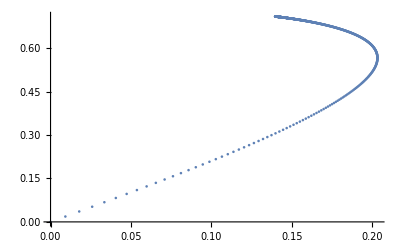

```mathematica
Show[
ListPlot[extragradOrbitData],
StreamPlot[V[x,y],{x,0,1},{y,0,1},StreamColorFunction->(ColorData["Rainbow",Norm[{#1,#2}]]&),
PlotTheme->"Scientific"]
]
```

### Convergence Speed

```mathematica
MeritPlot[projection_]:=Switch[projection,
"distance",extragradDistanceData,
"gradient norm",extragradGradientData];
```

```mathematica
Dynamic[
ListLogPlot[
MeritPlot[projectionType],
Joined->True,
Frame->True,
PlotRange->All,
GridLines->Automatic,
GridLinesStyle-> LightGray,
PlotTheme->"Scientific",
PlotStyle->{
{Darker[Red],AbsoluteThickness[1]}
},
PlotLabel->PopupMenu[Dynamic[projectionType],{"distance","gradient norm"}],
AspectRatio->1/GoldenRatio,
ImageSize->Large]]
```